/Users/eliasberriochoaesnaola

Piecewise[{{1, 0≥Re[z]}, {0, True}}]

{Listable}

1000

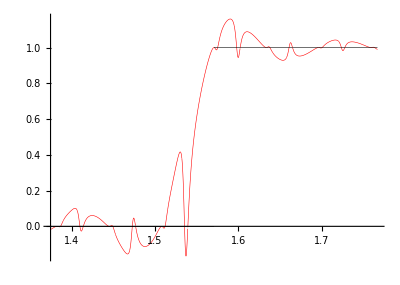

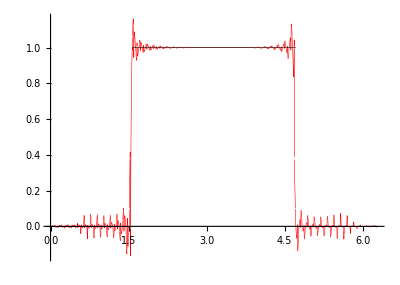

```mathematica
directorio=Directory[]
ftest[z_]=Piecewise[{{1,0>=Re[z]},{0,Re[z]<=0}}]


Attributes[ftest]={Listable}



(* szego.wls obtains the system of arcs related with the root of a paraothogonal polynomial  and write it as arcosalpha *)

n=100;T=2*Pi;
(*  Choice the Model

Get["Dropbox/articulo2023/cardan.wls"]
Get["Dropbox/articulo2023/kepler.wls"]
Get["Dropbox/articulo2023/random.wls"]
*)
Get["Dropbox/articulo2023/szego.wls"]



(* arcos.wls obtains all the system of arcs related with arcosalpha in the sense of the paper and the related nodal systems *)
Get["Dropbox/atypeofinterpolation2023/arcos.wls"]

(* derivadas.wls obtains the derivatives used in the paper for a nodal system in T *)
listaalpha=alphaW2n;listaarcosalpha=arcosalphaW2n;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];

derivadasalphaW2n=derivadas;
derivadassegundasalphaW2n=derivadas*factoresderivadassegundas;

(* same comment as before *)
listaalpha=alphaYn;listaarcosalpha=arcosalphaYn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];

derivadasalphaYn=derivadas;
derivadassegundasalphaYn=derivadas*factoresderivadassegundas;




(* same comment as before *)
listaalpha=alphaZn;listaarcosalpha=arcosalphaZn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaZn=derivadas;
derivadassegundasalphaZn=derivadas*factoresderivadassegundas;

(* u and v in the sense of the paper *)
u=ftest[alphaW2n];

(* semi Hermite and semi Hermite-Fejer interpolants using the barycentric formulae*)
Print[1000]
SHFejer[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));



BB1=Plot[{Re[SHFejer[E^(I x)]],Re[ftest[E^(I x)]]},{x,Pi/2-Pi/16,Pi/2+Pi/16},PlotPoints->800,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7]


CC=Plot[{Re[SHFejer[E^(I x)]],Re[ftest[E^(I x)]]},{x,0,2Pi},PlotPoints->800,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7]
```